## π^+→ μ^+ν_μ γ

### Functions

```mathematica
Clear[IB,SDP,SDM,SINTP,SINTM,dBdxdy,dBdsdt,StoX,TtoY]
```

```mathematica
IB[x_,y_]:=((1-y+r)/(x^2(x+y-1-r)))(x^2+2(1-x)(1-r)-(2x r(1-r))/(x+y-1-r));
SDP[x_,y_]:=(x+y-1-r)((x+y-1)(1-x)-r);
SDM[x_,y_]:=(1-y+r)(r+(1-x)(1-y));
SINTP[x_,y_]:=((1-y+r)/(x(x+y-1-r)))((1-x)(1-x-y)+r);
SINTM[x_,y_]:=((1-y+r)/(x(x+y-1-r)))(x^2-(1-x)(1-x-y)-r);

dBdxdy[x_,y_]:=α/(2π)1/(1-r)^2(IB[x,y]+1/r(M/(2 fp))^2((v+a)^2 SDP[x,y]+(v-a)^2 SDM[x,y])+
M/fp((v+a)SINTP[x,y]+(v-a)SINTM[x,y]));
```

s=(P-p_γ)^2=(Q-E_γ;p_γ)^2=(Q-E_γ)^2-E_γ^2=Q^2-2 E_γ Q=Q^2(1-x)
t=(P-p_μ)^2=(Q-E_μ;p_μ)^2=(Q-E_μ)^2-E_μ^2+m_μ^2=Q^2(1-y+β)

```mathematica
mpi^2(1-x)
```

```mathematica
xx[s_,t_]:=1-s/M^2;
yy[s_,t_]:=1-t/M^2+r;

e1[s_]:=(M^2-s)/(2M);
e2[t_]:=(M^2(1+r)-t)/(2M);
JacST = Det[{{D[xx[s,t],s],D[xx[s,t],t]},{D[yy[s,t],s],D[yy[s,t],t]}}];
```

```mathematica
dBdsdt[s_,t_]:=JacST*dBdxdy[xx[s,t],yy[s,t]];
```

```mathematica
dBdsdt[s,t]//Simplify
```

1/(2 π M^4 (r-1)^2)α ((t (a-v)^2 (M^4 r-M^2 r s+s t)-(a+v)^2 (M^2-s-t) (M^4 r-M^2 (r+1) s+s (s+t)))/(4 fp^2 M^4 r)+(t (a (M^4 (2 r-1)-2 M^2 r s+s (s+2 t))+v (M^2-s)^2))/(fp M (M^2-s) (M^2-s-t))-(t (M^6 (-2 r^2+2 r-1)+M^4 (2 r^2 s+s+t)-M^2 s (2 r s+2 r t+s)+s^2 (s+t)))/((M^2-s)^2 (-M^2+s+t)^2))

### Integration Bounds

```mathematica
Clear[E1,E2,m1,m2,m3,M];
```

```mathematica
E1=Eγ;
E2=Eμ;
m1=0;
m2=M √r;
m3=0;

repsEs={E1-> e1[s],E2-> e2[t]};

boundEqn=M^2+2E1 E2 + m1^2+m2^2-m3^2-2M(E1+E2)==2 √((E1^2-m1^2)(E2^2-m2^2))//ReplaceAll[#,repsEs]&;

sols=Solve[boundEqn,t];

tmin[s_]=sols⟦1,1,2⟧//Simplify
tmax[s_]=sols⟦2,1,2⟧//Simplify


Clear[E1,E2,m1,m2,m3,M,repsEs,boundEqn];
```

0

-(M^4 r)/s+M^2 (r+1)-s

### Integrate over t

```mathematica
int=Integrate[dBdsdt[s,t],t]//Simplify;
```

```mathematica
$Assumptions={0<x<1,r<1};

limhigh=(int//ReplaceAll[#,{t-> tmax[s]}]&);
limlow=(int//ReplaceAll[#,{t-> tmin[s]}]&);

limhigh-limlow//Simplify;

dndx=(M^2%)//ReplaceAll[#,s-> M^2(1-x)]&//PowerExpand//Simplify

$Assumptions=True;
```

Final expression for dN/dx

```mathematica
dndx
```

(α ((r+x-1) (M^2 x^4 (a^2+v^2) (r^2-r x+r-2 (x-1)^2)-12 fp M r (x-1) x^2 (a (r-2 x+1)+v x)-12 fp^2 r (x-1) (4 r (x-1)+(x-2)^2))+12 fp r (x-1)^2 log(r) (M x^2 (a (x-2 r)-v x)+fp (2 r^2-2 r x-x^2+2 x-2))-12 fp r (x-1)^2 log(1-x) (M x^2 (a (x-2 r)-v x)+fp (2 r^2-2 r x-x^2+2 x-2))))/(24 π fp^2 (r-1)^2 r (x-1)^2 x)

```mathematica
paramsmu={a-> 0.0119,v-> 0.0254,fp-> 92.2138,M-> 139.57018,α-> 0.0072971395213076475,r-> 0.573089627545656};
paramse={a-> 0.0119,v-> 0.0254,fp-> 92.2138,M-> 139.57018,α-> 0.0072971395213076475,r-> 0.003654075677196949};
```

### Final expressions for the spectra

```mathematica
dndee[e_]:=ReplaceAll[ReplaceAll[2/M dndx,x-> 2ee/M]/.paramse,ee-> e]
dndemu[e_]:=ReplaceAll[ReplaceAll[2/M dndx,x-> 2ee/M]/.paramsmu,ee-> e]
```

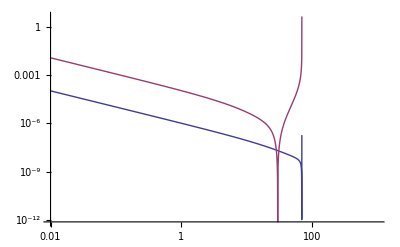

```mathematica
LogLogPlot[{0.000123*dndee[e],0.98*dndemu[e]},{e,10^-2,10^3}]
```

```mathematica
dnde[10^-2]
```

0.0119265

```mathematica
dndx//ReplaceAll[#,{fp-> Subscript[f, π],M-> Subscript[m, π],a-> A,v-> V}]&//StandardForm
```

1/(24 π (-1+r)^2 r (-1+x)^2 x f_π^2)α (12 r (-1+x)^2 Log[r] f_π ((-2+2 r^2+2 x-2 r x-x^2) f_π+x^2 (-V x+A (-2 r+x)) m_π)-12 r (-1+x)^2 Log[1-x] f_π ((-2+2 r^2+2 x-2 r x-x^2) f_π+x^2 (-V x+A (-2 r+x)) m_π)+(-1+r+x) (-12 r ((-2+x)^2+4 r (-1+x)) (-1+x) f_π^2-12 r (-1+x) x^2 (A (1+r-2 x)+V x) f_π m_π+(A^2+V^2) x^4 (r+r^2-2 (-1+x)^2-r x) m_π^2))

```mathematica
1/(24 π (-1+r)^2 r (-1+x)^2 x Subscript[f, π]^2)α //TeXForm
```

\frac{\alpha }{24 \pi  f_{\pi }^2 (r-1)^2 r (x-1)^2 x}

```mathematica
(-1+r+x) (-12 r ((-2+x)^2+4 r (-1+x)) (-1+x) Subscript[f, π]^2-12 r (-1+x) x^2 (A (1+r-2 x)+V x) Subscript[f, π] Subscript[m, π]+(A^2+V^2) x^4 (r+r^2-2 (-1+x)^2-r x) Subscript[m, π]^2)//Simplify//TeXForm
```

(r+x-1) \left(m_{\pi }^2 x^4 \left(A^2+V^2\right) \left(r^2-r x+r-2 (x-1)^2\right)-12
   f_{\pi } m_{\pi } r (x-1) x^2 (A (r-2 x+1)+V x)-12 f_{\pi }^2 r (x-1) \left(4 r
   (x-1)+(x-2)^2\right)\right)

```mathematica
12 r (-1+x)^2 Log[r/(1-x)] Subscript[f, π] ((-2+2 r^2+2 x-2 r x-x^2) Subscript[f, π]+x^2 (-V x+A (-2 r+x)) Subscript[m, π])//TeXForm
```

12 f_{\pi } r (x-1)^2 \log \left(\frac{r}{1-x}\right) \left(m_{\pi } x^2 (A (x-2 r)-V
   x)+f_{\pi } \left(2 r^2-2 r x-x^2+2 x-2\right)\right)

```mathematica
(2/M dndx)//ReplaceAll[#,{fp-> fpi,M-> mpi,a-> A,v-> V}]&//StandardForm
```

1/(12 fpi^2 mpi π (-1+r)^2 r (-1+x)^2 x)α ((-1+r+x) (-12 fpi^2 r ((-2+x)^2+4 r (-1+x)) (-1+x)+mpi^2 (A^2+V^2) x^4 (r+r^2-2 (-1+x)^2-r x)-12 fpi mpi r (-1+x) x^2 (A (1+r-2 x)+V x))+12 fpi r (-1+x)^2 (fpi (-2+2 r^2+2 x-2 r x-x^2)+mpi x^2 (-V x+A (-2 r+x))) Log[r]-12 fpi r (-1+x)^2 (fpi (-2+2 r^2+2 x-2 r x-x^2)+mpi x^2 (-V x+A (-2 r+x))) Log[1-x])

```mathematica
(2/M dndx)//ReplaceAll[#,{fp-> fpi,M-> mpi,a-> A,v-> V,α-> alphaem,x-> 2 egam/mpi}]&//FortranForm
```

(alphaem*((-1 + (2*egam)/mpi + r)*
     -       (-12*fpi**2*(-1 + (2*egam)/mpi)*r*
     -          ((-2 + (2*egam)/mpi)**2 + 4*(-1 + (2*egam)/mpi)*r) - 
     -         (48*egam**2*fpi*(-1 + (2*egam)/mpi)*r*
     -            (A*(1 - (4*egam)/mpi + r) + (2*egam*V)/mpi))/mpi + 
     -         (16*egam**4*(-2*(-1 + (2*egam)/mpi)**2 + r - (2*egam*r)/mpi + r**2)*
     -            (A**2 + V**2))/mpi**2) - 
     -      12*fpi*(-1 + (2*egam)/mpi)**2*r*
     -       (fpi*(-2 - (4*egam**2)/mpi**2 + (4*egam)/mpi - (4*egam*r)/mpi + 
     -            2*r**2) + (4*egam**2*(A*((2*egam)/mpi - 2*r) - (2*egam*V)/mpi))/mpi)
     -        *Log(1 - (2*egam)/mpi) + 
     -      12*fpi*(-1 + (2*egam)/mpi)**2*r*
     -       (fpi*(-2 - (4*egam**2)/mpi**2 + (4*egam)/mpi - (4*egam*r)/mpi + 
     -            2*r**2) + (4*egam**2*(A*((2*egam)/mpi - 2*r) - (2*egam*V)/mpi))/mpi)
     -        *Log(r)))/(24.*egam*fpi**2*(-1 + (2*egam)/mpi)**2*Pi*(-1 + r)**2*r)

```mathematica
dndx//ReplaceAll[#,x-> 2e/M]&//PowerExpand//FullSimplify[#,{0<e<M/2(1-r),0<r<1}]&//ReplaceAll[#,{fp-> fpi,M-> mpi,a-> A,v-> V,α-> alphaem,e-> egam}]&//FortranForm
```

(alphaem*(-2*(2*egam + mpi*(-1 + r))*
     -       (3*fpi**2*(2*egam - mpi)*mpi*r*
     -          ((egam - mpi)**2 + (2*egam - mpi)*mpi*r) - 
     -         3*egam**2*fpi*(2*egam - mpi)*mpi*r*
     -          (4*A*egam - A*mpi*(1 + r) - 2*egam*V) + 
     -         egam**4*(2*egam + mpi*(-1 + r))*(4*egam - mpi*(2 + r))*(A**2 + V**2))\
     -       + 3*fpi*mpi*(-2*egam + mpi)**2*r*
     -       (2*egam**2*fpi + 2*egam*fpi*mpi*(-1 + r) - 4*A*egam**2*(egam - mpi*r) - 
     -         fpi*mpi**2*(-1 + r**2) + 4*egam**3*V)*(Log(-2*egam + mpi) - Log(mpi*r))
     -      ))/(6.*egam*fpi**2*(1 - (2*egam)/mpi)**2*mpi**4*Pi*(-1 + r)**2*r)